```mathematica
data = Import["/net/home/f09/bajennissen/research/DAY196/sec_int_data/500nm.dat"]
```

{{1.64105,0.230159},{1.57964,0.233648},{1.51907,0.268881},{1.47433,0.273},{1.70936,0.23444},{1.78557,0.22833}}

0.480918-0.145952 x

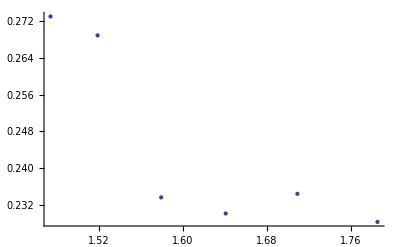

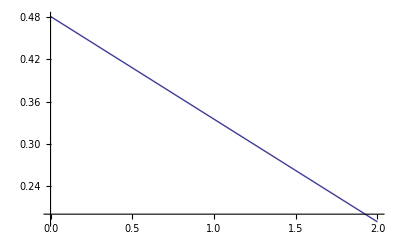

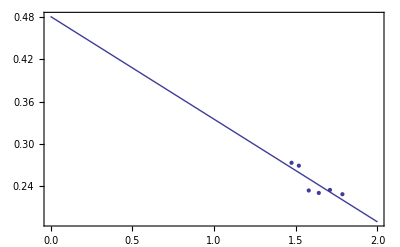

```mathematica
line = Fit[data,{1,x},x]
DataPlot=ListPlot[data]
FitPlot=Plot[line,{x,0,2}]
Show[DataPlot,FitPlot,PlotRange->All,Frame->True,AxesOrigin->{0,0}]
```